# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
f[{a_,b_}]:=Quiet[StringReplace[ToString[TeXForm[NumberForm[SetAccuracy[a±b,Accuracy[SetPrecision[b,2]]],ExponentFunction->(Null&)]]],"."->","]]
```

## Import Data

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]][[1;;-1]]
```

{D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=30.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=32.5.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=35.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=37.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=40.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=42.0.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=44.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=45.6.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=46.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=47.1.xlsx,D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Grundpraktikum\C1\Versuch 31\Durchfuhrung\Isotherm T=50.2.xlsx}

```mathematica
temps=(ToExpression@StringRiffle[StringSplit[StringSplit[#,"="][[-1]],"."][[1;;-2]],"."])&/@files
```

{30.1,32.5,35.,37.6,40.1,42.,44.1,44.6,45.1,45.6,46.1,47.1,50.2}

```mathematica
data=SortBy[Import[#][[1]],First]&/@files;
```

```mathematica
data=Map[{#[[1]]*10^(-6), #[[2]]*10^5, #[[3]]}&,data,{2}];
```

## Plotting

{Gas, Gemischt, Flüssig}

```mathematica
colours={RGBColor[0,0.6,0], RGBColor[0.56,0.37,0.60],Blue}
```

{RGBColor[0, 0.6, 0],RGBColor[0.56, 0.37, 0.6],RGBColor[0, 0, 1]}

```mathematica
states={"Gas", "Gemischt","Flüssig"}
```

{Gas,Gemischt,Flüssig}

```mathematica
assoc=AssociationThread[states,colours];
```

```mathematica
cf[_,_,_]=Black;
```

```mathematica
Do[((cf[i,x_,y_]/;(x-#[[1]])^2+(y-#[[2]])^2<=0.01=assoc[#[[3]]])&)/@data[[i]],{i,1,Length[data]}]
```

```mathematica
(*Do[cf[data[[i,j,1]],data[[i,j,2]]]=assoc[data[[i,j,3]]],{i,1,Length[data]},{j,1,Length[data[[i]]]}]*)
```

{Around[#[[1]],σv],Around[#[[2]],σP]} for error bars

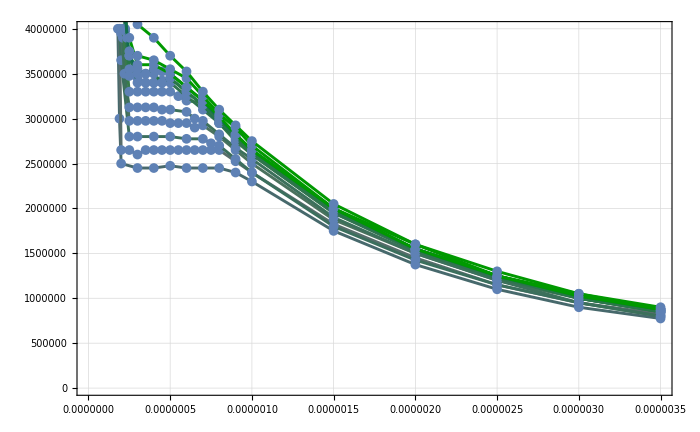

```mathematica
plts=Flatten@Table[{ListPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,Joined->True,pltsettings,PlotStyle->Thickness[0.003]],ListPlot[data[[i,All,1;;2]],ColorFunction->(cf[i,#1,#2]&),ColorFunctionScaling->False,PlotStyle->PointSize[0.01]]},{i,1,Length[data]}];
Show[plts]
```

## This is the final plot

```mathematica
(*plotMarkers->{Graphics[{Disk[{0,0},Scaled[0.02]]}],Graphics[{Disk[{0,0},Scaled[0.02]]}] }*)
```

```mathematica
plotMarkers=Charting`CommonDump`GraphicsOpenPlotMarkers[][[1;;3]];
```

```mathematica
plotMarkerAssoc=AssociationThread[states,plotMarkers];
```

```mathematica
flattened=Flatten[Map[#[[1;;3]]&, data,{2}],1];
```

```mathematica
pmarkers=plotMarkerAssoc[#[[3]]]&/@flattened;
```

```mathematica
cols=ColorData["ThermometerColors"]/@Rescale[temps];
```

```mathematica
pcolours=Flatten[Table[ConstantArray[cols[[i]],Length[data[[i]]]],{i,1,Length[data]}],1];
```

```mathematica
Show[ListPlot[Map[#[[1;;2]]&, data,{2}],PlotStyle->cols,pltsettings,Joined->True,PlotRange->All,PlotLegends->BarLegend[{ColorData["ThermometerColors"],{Min[temps],Max[temps]}},LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}]],ListPlot[Flatten[Map[{#[[1;;2]]}&, data,{2}],1],PlotMarkers->pmarkers,PlotStyle->pcolours]]
```

-Graphics-

## Fitting

```mathematica
R=8.314;
```

```mathematica
a0=0.8405;
b0=9.397/10^5;
n0=1.330/10^3;
```

```mathematica
a0=7.857/10;
b0=0.0879/1000;
n0=1.330/10^3;
```

```mathematica
temps[[-4]]
```

45.6

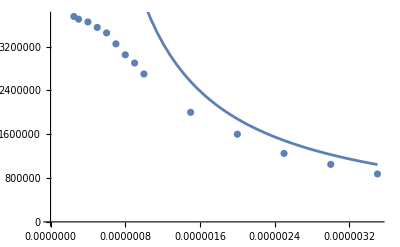

```mathematica
Show[ListPlot[{#[[1]],#[[2]]}&/@data[[-2]]], Plot[(n0 R (temps⟦-2⟧+273.15))/(V-n0 b0)-(n0^2 a0)/V,{V,0,3.5*10^(-6)}]]
```

```mathematica
fit=Table[{NonlinearModelFit[({#1⟦1⟧,#1⟦2⟧}&)/@data⟦i⟧,(n R (temps⟦i⟧+273.15-0.4))/(V-n b)-(n^2 a)/V^2,{{a,0.8405},{b,9.397/10^5},{n,1.330/10^3}},V],NonlinearModelFit[({#1⟦1⟧,#1⟦2⟧}&)/@data⟦i⟧,(n R (temps⟦i⟧+273.15))/(V-n b)-(n^2 a)/V^2,{{a,0.8405},{b,9.397/10^5},{n,1.330/10^3}},V],NonlinearModelFit[({#1⟦1⟧,#1⟦2⟧}&)/@data⟦i⟧,(n R (temps⟦i⟧+273.15+0.4))/(V-n b)-(n^2 a)/V^2,{{a,0.8405},{b,9.397/10^5},{n,1.330/10^3}},V]},{i,-4,-1}]
```

{{FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…]}}

## Processing Fit

```mathematica
qError[lst_]:={lst[[2]], Max[Abs[lst[[2]]-lst[[1]]], Abs[lst[[3]]-lst[[2]]]]}
```

```mathematica
rawVals=Table[Transpose[#["ParameterTableEntries"][[All,1]]&/@fit[[i]]],{i,1,Length[fit]}]
```

{{{0.773416,0.775361,0.777308},{0.0000838987,0.0000840041,0.0000841095},{0.00130235,0.00130071,0.00129908}},{{0.796832,0.798833,0.800836},{0.0000875231,0.0000876329,0.0000877427},{0.00135254,0.00135084,0.00134915}},{{0.775413,0.777354,0.779297},{0.0000843945,0.0000845,0.0000846056},{0.00135484,0.00135315,0.00135146}},{{0.777111,0.779038,0.780966},{0.0000860191,0.0000861257,0.0000862322},{0.00135237,0.00135069,0.00134902}}}

```mathematica
Map[StringReplace[ToString[#], "."->","]&, Table[{rawVals[[i,1]], 10^5 rawVals[[i,2]], 10^3 rawVals[[i,3]]},{i,1,Length[fit]}],{2}]
```

{{{0,773416, 0,775361, 0,777308},{8,38987, 8,40041, 8,41095},{1,30235, 1,30071, 1,29908}},{{0,796832, 0,798833, 0,800836},{8,75231, 8,76329, 8,77427},{1,35254, 1,35084, 1,34915}},{{0,775413, 0,777354, 0,779297},{8,43945, 8,45, 8,46056},{1,35484, 1,35315, 1,35146}},{{0,777111, 0,779038, 0,780966},{8,60191, 8,61257, 8,62322},{1,35237, 1,35069, 1,34902}}}

```mathematica
quantities=Table[qError/@Transpose[#["ParameterTableEntries"][[All,1]]&/@fit[[i]]],{i,1,Length[fit]}]
```

{{{0.775361,0.00194723},{0.0000840041,1.05417×10^-7},{0.00130071,1.63432×10^-6}},{{0.798833,0.00200303},{0.0000876329,1.09798×10^-7},{0.00135084,1.69465×10^-6}},{{0.777354,0.00194308},{0.0000845,1.05543×10^-7},{0.00135315,1.69223×10^-6}},{{0.779038,0.00192861},{0.0000861257,1.06542×10^-7},{0.00135069,1.67294×10^-6}}}

```mathematica
Table[{f[quantities[[i,1]]], f[10^5 quantities[[i,2]]], f[10^3 quantities[[i,3]]]},{i,1,Length[fit]}]
```

{{0,7754\pm 0,0019,8,400\pm 0,011,1,3007\pm 0,0016},{0,7988\pm 0,0020,8,763\pm 0,011,1,3508\pm 0,0017},{0,7774\pm 0,0019,8,450\pm 0,011,1,3531\pm 0,0017},{0,7790\pm 0,0019,8,613\pm 0,011,1,3507\pm 0,0017}}

```mathematica
1/{1,2,3,4}^2
```

{1,1/4,1/9,1/16}

```mathematica
Min[1,2]
```

1

```mathematica
processData[dat_]:=Module[{weights=1/Total[1/dat⟦All,2⟧^2], sum=Sum[dat[[i,1]]/dat[[i,2]]^2,{i,1,Length[dat]}],ave, err1,err2}, ave=sum weights; err1=Sqrt[weights];err2= 1/Sqrt[Length[dat](Length[dat]-1)] Sqrt[Sum[(dat[[i,1]]-ave)^2,{i,1,Length[dat]}]]; {ave, Max[err1,err2],err1, err2}]
```

```mathematica
qdata=processData/@Transpose[quantities]
```

{{0.782399,0.00544945,0.000977441,0.00544945},{0.0000855218,8.25068×10^-7,5.33909×10^-8,8.25068×10^-7},{0.00133824,0.0000127297,8.36502×10^-7,0.0000127297}}

```mathematica
f[qdata[[1,1;;2]]]
f[10^5 qdata[[2,1;;2]]]
f[10^3qdata[[3,1;;2]]]
```

0,7824\pm 0,0054

8,552\pm 0,083

1,338\pm 0,013

```mathematica
cols2=ColorData["ThermometerColors"]/@Rescale[temps[[-4;;-1]]];
```

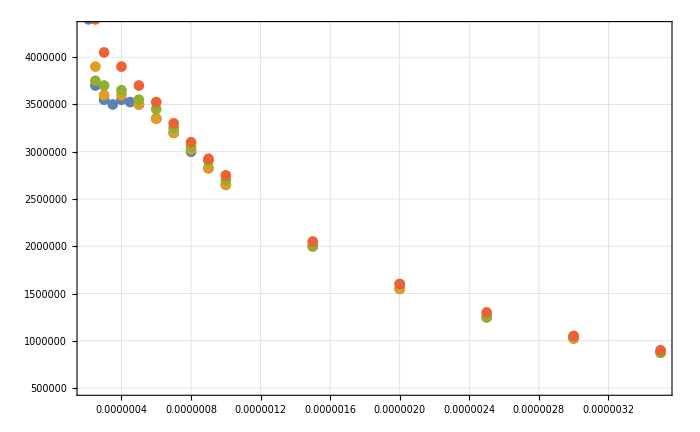

```mathematica
Show[ListPlot[data[[-4;;-1,All,{1,2}]]],Plot[Evaluate[#[t]&/@fit],{t,1.5*10^(-7),3.5*10^(-6)}],PlotRange->{All,{0.5*10^6,4.3*10^6}},pltsettings]
```

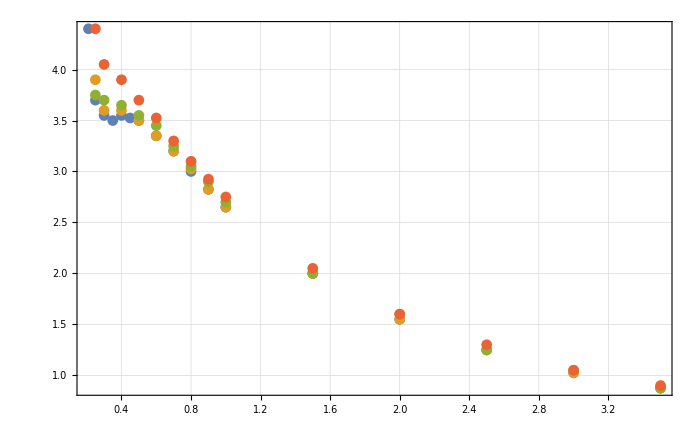

```mathematica
Show[ListPlot[Map[{#[[1]]*10^6,#[[2]]*10^(-6)}&,data[[-4;;-1,All,{1,2}]],{2}]],Plot[Evaluate[10^(-6)#[t*10^(-6)]&/@fit],{t,0,3.5}],PlotRange->{All,{Automatic,4.3}},pltsettings]
```

## Things

```mathematica
anew=qdata[[1,1]]
```

0.782399

```mathematica
Δanew=qdata[[1,2]]
```

0.00544945

```mathematica
bnew=qdata[[2,1]]
Δbnew=qdata[[2,2]]
```

0.0000855218

8.25068×10^-7

```mathematica
nnew=qdata[[3,1]]
Δnnew=qdata[[3,2]]
```

0.00133824

0.0000127297

## Critical Point

```mathematica
Vk=3 nnew bnew
ΔVk=Sqrt[(3 bnew Δnnew)^2 + (3 nnew Δbnew)^2]
```

3.43345×10^-7

4.65176×10^-9

```mathematica
f[{Vk, ΔVk}*10^6]
```

0,3433\pm 0,0047

```mathematica
Pk=anew/(27 bnew^2)
ΔPk=√((Δanew/(27 bnew^2))^2+((2 anew Δbnew)/(27 bnew^3))^2)
```

3.96196×10^6

81273.9

```mathematica
f[{Pk, ΔPk}10^(-5)]
```

39,62\pm 0,81

```mathematica
Tk=(8 anew)/(27 R bnew)
```

326.037

```mathematica
ΔTk=Sqrt[((8 Δanew)/(27 R bnew))^2+((8 anew)/(27 R bnew^2)Δbnew)^2]
```

3.87951

```mathematica
f[{Tk, ΔTk}]
f[{Tk-273.15, ΔTk}]
```

326,0\pm 3,9

52,9\pm 3,9

```mathematica
(Pk Vk)/(nnew R Tk)
```

0.375

```mathematica
Vk*10^6
ΔVk *10^6
```

0.343345

0.00465176

```mathematica
Pk*10^(-5)
ΔPk*10^(-5)
```

39.6196

0.812739

```mathematica
Tk-273.15
```

52.8874